```mathematica
ClearAll["Global`*"];

G = 6.67 * 10^-11;

Mz = 5.96 * 10^24;

m=1500;

FG = G * (m*Mz)/R^2;

Fod = (m * v^2) /R;

Ek = (m * v^2) / 2;

EpR = -G * (m * Mz) / R;
```

```mathematica
r1 = Solve[Fod ==FG,v]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{v→-(1.99382×10^7)/(√R)},{v→(1.99382×10^7)/(√R)}}

```mathematica
Ekc[R_]=Ek/.r1[[2,1]]

EpRc[R_]=EpR/.r1[[2,1]]
```

(2.98149×10^17)/R

-(5.96298×10^17)/R

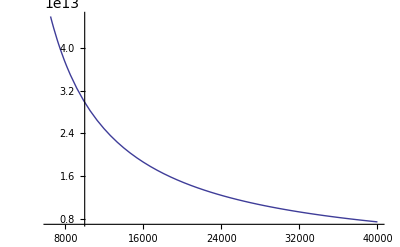

```mathematica
Plot[Ekc[R],{R, 6500, 40000}]
```

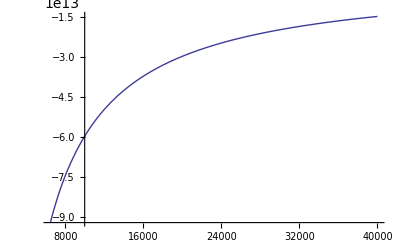

```mathematica
Plot[EpRc[R],{R, 6500, 40000}]
```